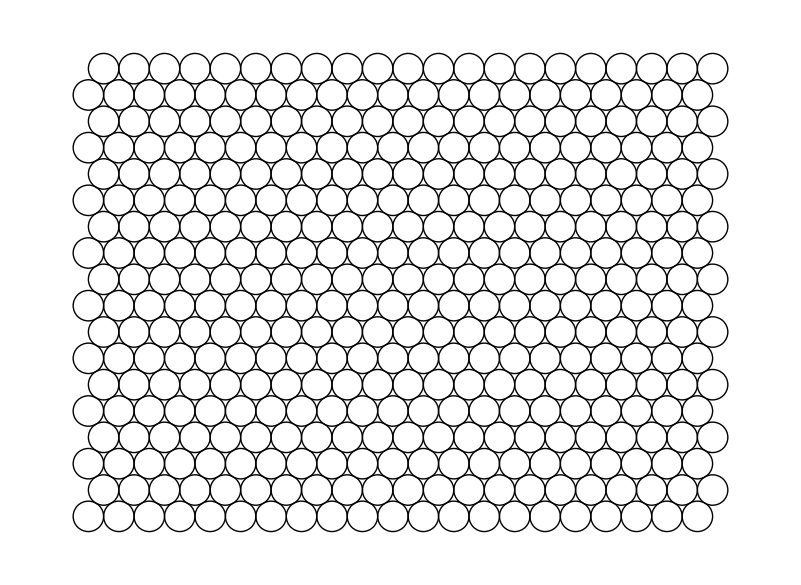

{{{2,0},{2,2 √3},{2,4 √3},{2,6 √3},{2,8 √3}},{{4,0},{4,2 √3},{4,4 √3},{4,6 √3},{4,8 √3}},{{6,0},{6,2 √3},{6,4 √3},{6,6 √3},{6,8 √3}},{{8,0},{8,2 √3},{8,4 √3},{8,6 √3},{8,8 √3}},{{10,0},{10,2 √3},{10,4 √3},{10,6 √3},{10,8 √3}},{{12,0},{12,2 √3},{12,4 √3},{12,6 √3},{12,8 √3}},{{14,0},{14,2 √3},{14,4 √3},{14,6 √3},{14,8 √3}},{{16,0},{16,2 √3},{16,4 √3},{16,6 √3},{16,8 √3}},{{18,0},{18,2 √3},{18,4 √3},{18,6 √3},{18,8 √3}},{{20,0},{20,2 √3},{20,4 √3},{20,6 √3},{20,8 √3}},{{22,0},{22,2 √3},{22,4 √3},{22,6 √3},{22,8 √3}},{{24,0},{24,2 √3},{24,4 √3},{24,6 √3},{24,8 √3}},{{26,0},{26,2 √3},{26,4 √3},{26,6 √3},{26,8 √3}},{{28,0},{28,2 √3},{28,4 √3},{28,6 √3},{28,8 √3}},{{30,0},{30,2 √3},{30,4 √3},{30,6 √3},{30,8 √3}}}

```mathematica
a=Table[Circle[{2*i,2*Sqrt[3]*j},1],{i,-10,10},{j,-4,4}];
b=Table[Circle[{2*i+1,Sqrt[3]*(2*j+1)},1],{i,-10,10},{j,-4,4}];
c=Flatten[{a,b}];
Show@Graphics@c
a=Table[{2*i,2*Sqrt[3]*j},{i,1,15},{j,0,4}];
b=Table[{2*i+1,Sqrt[3]*(2*j+1)},{i,1,15},{j,0,4}];
a
```

```mathematica
k=10;
dist=(#1[[1]]-#2[[1]])^2+(#1[[2]]-#2[[2]])^2&;
a=Table[{2*i,2*Sqrt[3]*j},{i,-k,k},{j,-k,k}];
b=Table[{2*i+1,Sqrt[3]*(2*j+1)},{i,-k,k},{j,-k,k}];
all=Flatten[{Flatten[a,1],Flatten[b,1]},1];
distrull=dist[#,{0,0}]&;
Sort[distrull/@all,#1<#2&]
```

{0,4,4,4,4,4,4,12,12,12,12,12,12,16,16,16,16,16,16,28,28,28,28,28,28,28,28,28,28,28,28,36,36,36,36,36,36,48,48,48,48,48,48,52,52,52,52,52,52,52,52,52,52,52,52,64,64,64,64,64,64,76,76,76,76,76,76,76,76,76,76,76,76,84,84,84,84,84,84,84,84,84,84,84,84,100,100,100,100,100,100,108,108,108,108,108,108,112,112,112,112,112,112,112,112,112,112,112,112,124,124,124,124,124,124,124,124,124,124,124,124,144,144,144,144,144,144,148,148,148,148,148,148,148,148,148,148,148,148,156,156,156,156,156,156,156,156,156,156,156,156,172,172,172,172,172,172,172,172,172,172,172,172,192,192,192,192,192,192,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,208,208,208,208,208,208,208,208,208,208,208,208,228,228,228,228,228,228,228,228,228,228,228,228,244,244,244,244,244,244,244,244,244,244,244,244,252,252,252,252,252,252,252,252,252,252,252,252,256,256,256,256,256,256,268,268,268,268,268,268,268,268,268,268,268,268,292,292,292,292,292,292,292,292,292,292,292,292,300,300,300,300,300,300,304,304,304,304,304,304,304,304,304,304,304,304,316,316,316,316,316,316,316,316,316,316,316,316,324,324,324,324,324,324,336,336,336,336,336,336,336,336,336,336,336,336,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,372,372,372,372,372,372,372,372,372,372,372,372,388,388,388,388,388,388,388,388,388,388,388,388,400,400,400,400,400,400,412,412,412,412,412,412,412,412,412,412,412,412,432,432,432,432,432,432,436,436,436,436,436,436,436,436,436,436,436,436,444,444,444,444,444,444,444,444,444,444,448,448,448,448,448,448,448,448,448,448,448,448,468,468,468,468,468,468,468,468,468,468,484,484,484,484,496,496,496,496,496,496,496,496,508,508,508,508,508,508,508,508,508,508,508,508,516,516,516,516,516,516,516,516,516,516,532,532,532,532,532,532,532,532,532,532,532,532,532,532,532,532,556,556,556,556,556,556,556,556,576,576,576,576,588,588,588,588,588,588,588,588,588,588,588,588,592,592,592,592,592,592,592,592,604,604,604,604,604,604,604,604,624,624,624,624,624,624,624,624,628,628,628,628,628,628,628,628,652,652,652,652,652,652,652,652,676,676,676,676,676,676,676,676,684,684,684,684,684,684,688,688,688,688,688,688,688,688,700,700,700,700,700,700,700,700,724,724,724,724,724,724,724,724,732,732,732,732,732,732,732,732,756,756,756,756,756,756,756,756,768,768,772,772,772,772,784,784,784,784,784,784,784,784,796,796,796,796,796,796,796,796,804,804,804,804,804,804,832,832,832,832,832,832,832,832,844,844,844,844,844,844,844,844,868,868,868,868,868,868,868,868,868,868,868,868,876,876,876,876,892,892,892,892,900,900,900,900,912,912,912,912,912,912,912,912,916,916,916,916,948,948,948,948,948,948,964,964,964,964,964,964,964,964,972,972,976,976,976,976,988,988,988,988,988,988,988,988,988,988,988,988,1008,1008,1008,1008,1024,1024,1024,1024,1036,1036,1036,1036,1036,1036,1036,1036,1036,1036,1036,1036,1072,1072,1072,1072,1084,1084,1084,1084,1092,1092,1092,1092,1092,1092,1092,1092,1092,1092,1092,1092,1108,1108,1108,1108,1116,1116,1116,1116,1116,1116,1132,1132,1132,1132,1156,1156,1156,1156,1164,1164,1164,1164,1168,1168,1168,1168,1168,1168,1168,1168,1200,1200,1204,1204,1204,1204,1204,1204,1204,1204,1216,1216,1216,1216,1228,1228,1228,1228,1228,1228,1228,1228,1236,1236,1236,1236,1252,1252,1252,1252,1264,1264,1264,1264,1296,1296,1296,1296,1300,1300,1300,1300,1308,1308,1308,1308,1308,1308,1324,1324,1332,1332,1344,1344,1344,1344,1348,1348,1372,1372,1372,1372,1372,1372,1372,1372,1372,1372,1396,1396,1396,1396,1404,1404,1444,1444,1444,1444,1444,1444,1456,1456,1456,1456,1492,1492,1524,1524,1524,1524,1524,1524,1548,1548,1600,1600,1600,1600,1612,1612,1684,1684,1764}

```mathematica
3.405*2^(1/6)
```

3.82198